```mathematica
s=NDSolve[{0.1 x''[t]+7x'[t]+100x[t]==0 ,x[0]==0,x'[0]==100},x,{t,0,1}]
```

{{x→InterpolatingFunction[…]}}

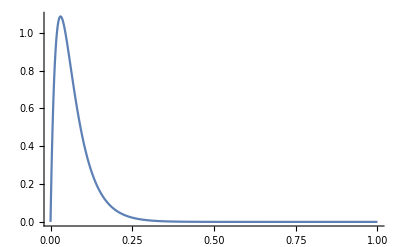

```mathematica
Plot[Evaluate[x[t]/.s],{t,0,1}, PlotRange->All]
```

```mathematica
(4*0.1*100)^.5
```

6.32456